FittedModel[-0.000469307+0.000154935 x]

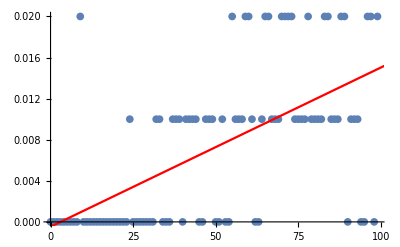

0.665205

{0.697963,5.64742×10^-11}

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "name"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, a+b*x,{a,b},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
nlm["ParameterPValues"]
```